{1.44618,1.44407}

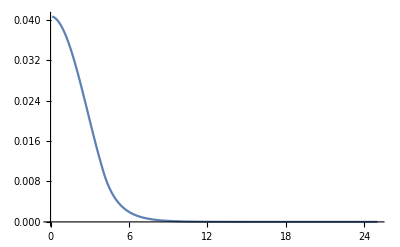

```mathematica
Clear["Global`*"]

NN=201;
rMax=25;
h=rMax/NN;

nMat=1.444;
k0=2Pi/1.55;
l=0;

RIP=Array[(0.0036HeavisideTheta[8.2/2-h#]+1)nMat&,NN];

D1=DiagonalMatrix[ConstantArray[-1/2,NN-1],-1]+DiagonalMatrix[ConstantArray[1/2,NN-1],1];
D1[[1]]=PadRight[{-3/2,2,-1/2},NN];
D1[[-1]]=PadLeft[{1/2,-2,3/2},NN];

D2=Normal[SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{NN,NN}]];
D2[[1]]=PadRight[{2,-5,4,-1},NN];
D2[[-1]]=PadLeft[{-1,4,-5,2},NN];

DivByr=Array[1/h/#&,NN];

{β,Modes}=Eigensystem[D2/h^2+1/h D1 DivByr-l^2DivByr^2 IdentityMatrix[NN]+k0^2 RIP^2 IdentityMatrix[NN]];
β=Sqrt[β];

TrueModesNEff=Chop[Select[β/k0,Re[#]>nMat&] ](*Не самый точный и правильный критерий*)

ListPlot[Abs[Modes[[130]]]^2,PlotRange->All,DataRange->{h,rMax},Joined->True]
```

Домашнее задание

1) Изучить синтаксис операторов: Table, Array, PadRight, PadLeft, SparseArray, Band, Normal, DataRange, Select. Изучить понятие PureFunction, Patterns
2) Изучить https://en.wikipedia.org/wiki/Finite_difference_coefficient . Уметь объяснить расчет одно- и двусторонних коэффициентов для произвольной производной произвольного порядка сходимости.
3) Найти коэффициенты Селлмейера для плавленого кварца. Построить кривую показателя преломления по этой формуле и построить кривую материальной ДГС в зависимости от длины волны.
	Дисперсия групповых скоростей в волокне может выражаться в двух величинах: β2 [пс2/км] и d [пс/нм/км]. Построить график ДГС для обоих случаев. Знать формулу, связывающую β2 и d с dn/dλ.
	Знать определение понятий аномальная/нормальная дисперсия, аномальная/нормальная дисперсия групповых скоростей
	Дать физическую интерпретацию величины дисперсии 1 пс/нм/км. Например, физическая интерпретация величины тока в 1 А – «есть сила неизменяющегося тока, который при прохождении по двум параллельным прямолинейным проводникам бесконечной длины и ничтожно малой площади кругового поперечного сечения, расположенным в вакууме на расстоянии 1 метр один от другого, вызвал бы на каждом участке проводника длиной 1 метр силу взаимодействия, равную 2·10^-7 ньютона». Подсказка: как можно понять из размерности, в интерпретации будут слова «пикосекунда», «нанометр» и «километр».
4) Придумать свою функцию, которая на вход принимает массив собственных чисел, а на выходе выдает номера физически осмысленных мод
	Придумать свой критерий физической осмысленности. Проверить критерий для разных конфигураций ППП. Уметь обосновать выбор такого критерия 
	Использовать оператор Position и Patterns
5) Уметь нарисовать на бумажке приблизительно график интенсивности в поперечном сечении волокна для мод LP_lm. Также уметь по графику назвать числа l и m 
6) Численно решить трансцендентное характеристическое уравнение для нахождения собственных мод для ППП - ступеньки (взять данные для волокна SMF28). Найти nEff, построить найденные моды.
	Сравнить два решения: через характеристическое уравнение и через дискретизацию ППП (как на семинаре)
	Дать определение длины волны отсечки
	Уметь найти длину волны отсечки с помощью решения характеристического уравнения
	Дать определение нормализованной частоты. Проверить совпадение нормализованной частоты и найденной длины волны отсечки.
	Порядок возникновения LP мод в волокне “ступенька” при уменьшении длины волны. Как порядок зависит от параметров ступеньки?
7)  В файле SMF28.xlsx содержится набор экспериментальных точек, описывающих ППП у волокна SMF28. Найти моды для такого ППП.
	Обработать экспериментальные данные, привести их к функции n(r)
	Рассчитать моды в таком волокне, используя свой критерий отсева нефизичных мод
	Найти длину волны отсечки в волокне. Как она зависит от вашего критерия?
	Отнормировать моды на пиковую интенсивность, равную 1 Вт/м^2
	Отнормировать моды так, чтобы ∫|Ψ|^2ds = 1 (не забыть Якобиан) . ds - дифференциал площади поперечного сечения волокна
8) Посчитать число приближений и упрощений, используемое в выводе уравнения на собственные моды волокна. Знать, для чего нужно каждое приближение